```mathematica
Sigma[0] = SparseArray[IdentityMatrix[2]];
Sigma[1] = SparseArray[{{0, 1}, {1, 0}}];
Sigma[2] = SparseArray[{{0, -I}, {I, 0}}];
Sigma[3] = SparseArray[{{1, 0}, {0, -1}}];
Sigma[4]= (Sigma[1]+ I*Sigma[2])/2;
Sigma[5]= (Sigma[1]- I*Sigma[2])/2;
```

```mathematica
Commutator[A_, B_]:= A.B - B.A
```

```mathematica
PauliOp[pList_]:= KroneckerProduct@@Table[Sigma[pList[[i]]], {i, 1, Length[pList]}]
```

## Square lattice on 2D 2x2 torus

```mathematica
HTC2[Je_, Jm_]:=-Je(PauliOp[{3, 3, 0, 0, 3, 3, 0, 0}]+PauliOp[{3, 0, 0, 3, 3, 0, 0, 3}]+PauliOp[{0, 3, 3, 0, 0, 3, 3, 0}]+PauliOp[{0, 0, 3, 3, 0, 0, 3, 3}])-Jm(PauliOp[{1, 1, 1, 1, 0, 0, 0, 0}]+PauliOp[{0, 1, 0, 1, 1, 0, 1, 0}]+PauliOp[{1, 0, 1, 0, 0, 1, 0, 1}]+PauliOp[{0, 0, 0, 0, 1, 1, 1, 1}])
```

```mathematica
{evals, evecs}= Eigensystem[HTC2[1, 1]//Normal];
Esys = Transpose[{evals,evecs}];
Esys=Transpose[SortBy[Esys,First]];
GSs = Normalize/@Esys[[2, 1;;4]];
```

```mathematica
H=HTC2[1, 1];
GSs[[1]].H.GSs[[1]]
```

-8

```mathematica
HQED2[Je_, Jm_, γ_]:=HTC2[Je, Jm]-γ(PauliOp[{4, 4, 4, 4, 0, 0, 0, 0}]+PauliOp[{0, 4, 0, 4, 4, 0, 4, 0}]+PauliOp[{4, 0, 4, 0, 0, 4, 0, 4}]+PauliOp[{0, 0, 0, 0, 4, 4, 4, 4}]+PauliOp[{5, 5, 5, 5, 0, 0, 0, 0}]+PauliOp[{0, 5, 0, 5, 5, 0, 5, 0}]+PauliOp[{5, 0, 5, 0, 0, 5, 0, 5}]+PauliOp[{0, 0, 0, 0, 5,5, 5, 5}]-(PauliOp[{1, 1, 1, 1, 0, 0, 0, 0}]+PauliOp[{0, 1, 0, 1, 1, 0, 1, 0}]+PauliOp[{1, 0, 1, 0, 0, 1, 0, 1}]+PauliOp[{0, 0, 0, 0, 1, 1, 1, 1}]))
```

### Plot the change of the ground state energy of H_QED turning on γ from 0 to 1

Eigenvalues::arh: Because finding 256 out of the 256 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

General::stop: Further output of Eigenvalues::arh will be suppressed during this calculation.

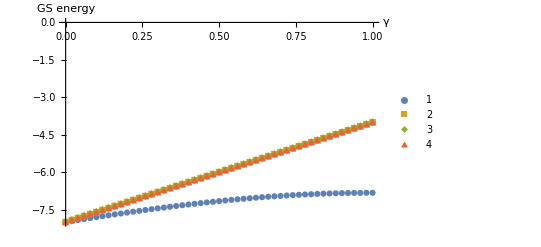

```mathematica
ListPlot[Table[{γ, Sort[Eigenvalues[HQED2[1, 1, γ]]][[i]]},{i, 1, 4}, {γ, 0, 1, 0.02}], PlotLegends->Automatic, AxesLabel-> {"γ", "GS energy"}, PlotMarkers->Automatic]
```

```mathematica
eigenvectorQ[matrix_,vector_]:=MatrixRank[{matrix.vector,vector}]==1
```

```mathematica
eigenvectorQ[HQED2[1, 1, 1], GSs[[4]]]
```

False

```mathematica
GSs[[i]]
```

{{-2,2,0,0},{{1,0,0,1},{0,-1,1,0},{-1,0,0,1},{0,1,1,0}}}

```mathematica
HQED4[Jm_]:=-Jm(PauliOp[{4, 4, 4, 4, 0, 0, 0, 0}]+PauliOp[{0, 4, 0, 4, 4, 0, 4, 0}]+PauliOp[{4, 0, 4, 0, 0, 4, 0, 4}]+PauliOp[{0, 0, 0, 0, 4, 4, 4, 4}]+PauliOp[{5, 5, 5, 5, 0, 0, 0, 0}]+PauliOp[{0, 5, 0, 5, 5, 0, 5, 0}]+PauliOp[{5, 0, 5, 0, 0, 5, 0, 5}]+PauliOp[{0, 0, 0, 0, 5,5, 5, 5}])
```

```mathematica
{evals, evecs}= Eigensystem[HQED4[1]//Normal];
Esys = Transpose[{evals,evecs}];
Esys=Transpose[SortBy[Esys,First, Less]];
Esys[[1]]
Esys[[2, 1]]
Esys[[2, 256]]
```

{-2 √2,-2,-2,-√2,-√2,-√2,-√2,-√2,-√2,-√2,-√2,-√2,-√2,-√2,-√2,-√2,-√2,-√2,-√2,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,√2,√2,√2,√2,√2,√2,√2,√2,√2,√2,√2,√2,√2,√2,√2,√2,2,2,2 √2}

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/(√2),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/(√2),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/(√2),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/(√2),0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/(√2),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/(√2),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/(√2),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/(√2),0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}

```mathematica
HQED2[Jm_]:=-Jm(PauliOp[{4, 4, 4, 4, 0, 0, 0}]+PauliOp[{ 0, 0, 0, 4, 4, 4, 4}]+PauliOp[{5, 5, 5, 5, 0, 0, 0}]+PauliOp[{0, 0, 0, 5,5, 5, 5}])
```

```mathematica
{evals, evecs}= Eigensystem[HQED2[1]//Normal];
Esys = Transpose[{evals,evecs}];
Esys=Transpose[SortBy[Esys,First, Less]];
Esys[[1]]
BaseForm[Position[Esys[[2, 1]],  _?(#≠0&)]-1, 2]
BaseForm[Position[Esys[[2, 2]],  _?(#≠0&)]-1, 2]
```

{-√2,-√2,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,√2,√2}

{{0_2,0_2},{0_2,1_2},{0_2},{1111_2},{1111000_2}}

{{111_2,0_2},{111_2,1_2},{111_2},{1110000_2,0_2},{1110000_2,1_2},{1110000_2},{1111111_2}}

Eigenvalues::arhm: Because finding 256 out of the 256 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors at machine precision would be sufficient, consider using N on the matrix and restricting this number using the second argument to Eigenvalues.

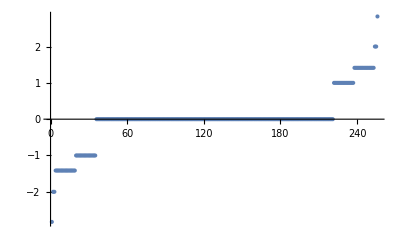

```mathematica
ListPlot[Sort[Eigenvalues[HQED4[1]], Less]]
```

## Partial trace (from Mark Tame’s notebook https://library.wolfram.com/infocenter/MathSource/5571/)

```mathematica
SwapParts[expr_, pos1_, pos2_] := ReplacePart[#,#, {pos1,pos2}, {pos2,pos1}]&[expr]
TraceSystem[D_, s_]:= (

Qubits=Reverse[Sort[s]];
TrkM=D;

z=(Dimensions[Qubits][[1]]+1);

For[q=1,q<z,q++,
n=Log[2,(Dimensions[TrkM][[1]])];
M=TrkM;
k=Qubits[[q]];
If[k==n,
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];
 ],
For[j=0,j<(n-k),j++,
b={0};
For[i=1,i<2^n+1,i++,
If[(Mod[(IntegerDigits[i-1,2,n][[n]]+IntegerDigits[i-1,2,n][[n-j-1]]),2])==1 && Count[b, i]  ==0, Permut={i,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)};
b=Append[b,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)];
c=Range[2^n];
perm=SwapParts[c,{i},{(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)}];

M=M[[perm,perm]];

 ]    
]         ;
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];
]
   ];
]

]

;Return[TrkM])
```

## Entanglement (von Neumann) Entropy: -Tr[ρ_A log(ρ_A)]

```mathematica
EE[D_]:=(
Non0Evals = DeleteCases[Eigenvalues[D], 0];
ee=-Total[ Non0Evals*Log[Non0Evals]];
Return[ee];)
```

### E.g. for bell state (S_A = log2)

```mathematica
RhoBell = Outer[Times, {1/Sqrt[2], 0, 0, 1/Sqrt[2]}, {1/Sqrt[2], 0, 0, 1/Sqrt[2]}];
RhoA = TraceSystem[RhoBell, {2}];
SA = EE[RhoA]
```

Log[2]

### GHZ state

```mathematica
RhoBell = Outer[Times, {1/Sqrt[2], 0, 0, 0, 0, 0, 0, 1/Sqrt[2]}, {1/Sqrt[2], 0, 0, 0, 0, 0, 0, 1/Sqrt[2]}];
RhoA = TraceSystem[RhoBell, {2}];
SA = EE[RhoA]
```

Log[2]

### W state

```mathematica
RhoBell = Outer[Times, {0, 1/Sqrt[3], 1/Sqrt[3], 0, 1/Sqrt[3], 0, 0, 0}, {0, 1/Sqrt[3], 1/Sqrt[3], 0, 1/Sqrt[3], 0, 0, 0}];
RhoA = TraceSystem[RhoBell, {2}];
SA = EE[RhoA]
```

2/3 Log[3/2]+Log[3]/3

## Topological EE: S_topo = S_A + S_B + S_C - S_AB - S_AC - S_BC + S_ABC

```mathematica
TopoEE[ρ_,A_, B_, C_, ALL_]:= (
(* ρ: density matrix of the GS; A, B, C: list of qubits of the disjoint subspaces on the lattice*)
ρA=TraceSystem[ρ, Complement[ALL, A]];
ρB=TraceSystem[ρ, Complement[ALL, B]];
ρC=TraceSystem[ρ, Complement[ALL, C]];
ρAB=TraceSystem[ρ, Complement[ALL, Union[A, B]]];
ρAC=TraceSystem[ρ, Complement[ALL, Union[A, C]]];
ρBC=TraceSystem[ρ, Complement[ALL, Union[B, C]]];
ρABC=TraceSystem[ρ, Complement[ALL, Union[A, B, C]]];
Print[ρA];
Stopo = EE[ρA]+EE[ρB]+EE[ρC]-EE[ρAB]-EE[ρAC]-EE[ρBC]+EE[ρABC];
Return[Stopo];
)
```

```mathematica
ClearAll[ρA, ρB, ρC, ρAB, ρAC, ρBC, ρABC,Stopo]
```

### Topologocal EE of the toric code (must be 2log2 for toric code)

```mathematica
TopoEE[Outer[Times, GSs[[4]], Conjugate[GSs[[4]]]], {3, 4}, {7}, {8}, Table[i, {i, 1, 8}]]//Simplify
```

{{1/4,0,0,0},{0,1/4,0,0},{0,0,1/4,0},{0,0,0,1/4}}

-Log[2]

```mathematica
GSQED2 = Normalize[Eigenvectors[HQED2[1, 1, 1]][[1]]];
```

Eigenvectors::arhm: Because finding 256 out of the 256 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors at machine precision would be sufficient, consider using N on the matrix and restricting this number using the second argument to Eigenvectors.

```mathematica
TopoEE[Outer[Times, GSQED2, Conjugate[GSQED2]], {3, 4}, {7}, {8}]//Simplify
```

-Log[2]/2

```mathematica
HQED=PauliOp[{4, 4, 4, 4, 0, 0, 0, 0}]+PauliOp[{0, 4, 0, 4, 4, 0, 4, 0}]+PauliOp[{4, 0, 4, 0, 0, 4, 0, 4}]+PauliOp[{0, 0, 0, 0, 4, 4, 4, 4}]+PauliOp[{5, 5, 5, 5, 0, 0, 0, 0}]+PauliOp[{0, 5, 0, 5, 5, 0, 5, 0}]+PauliOp[{5, 0, 5, 0, 0, 5, 0, 5}]+PauliOp[{0, 0, 0, 0, 5,5, 5, 5}];
```

Eigenvectors::arhm: Because finding 256 out of the 256 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors at machine precision would be sufficient, consider using N on the matrix and restricting this number using the second argument to Eigenvectors.

```mathematica
GSQED = Normalize[Eigenvectors[HQED][[1]]];
```

Eigenvectors::arhm: Because finding 256 out of the 256 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors at machine precision would be sufficient, consider using N on the matrix and restricting this number using the second argument to Eigenvectors.

```mathematica
TopoEE[Outer[Times, GSQED, Conjugate[GSQED]], {3, 4}, {7}, {8}]//Simplify
```

-Log[2]/2

```mathematica
HZ2[Jm_]:=-Jm(PauliOp[{1, 1, 1, 1, 0, 0, 0, 0}]+PauliOp[{0, 1, 0, 1, 1, 0, 1, 0}]+PauliOp[{1, 0, 1, 0, 0, 1, 0, 1}]+PauliOp[{0, 0, 0, 0, 1, 1, 1, 1}])
GSZ2 = Normalize[Eigenvectors[HZ2[1]][[1]]];
```

Eigenvectors::arhm: Because finding 256 out of the 256 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors at machine precision would be sufficient, consider using N on the matrix and restricting this number using the second argument to Eigenvectors.

```mathematica
TopoEE[Outer[Times, GSZ2, Conjugate[GSZ2]], {3}, {7}, {4, 8}, Table[i, {i, 1, 8}]]//Simplify
```

{{1/2,0},{0,1/2}}

-Log[2]

```mathematica
BaseForm[SparseArray[GSQED2]["AdjacencyLists"]-1, 2]
```

{0_2,1111_2,1011010_2,10100101_2,11110000_2,11111111_2}

```mathematica
EEQED2 = EE[GSQED2,
```